```mathematica
guneqn=Aaa 10^43 ((4 π)/3 r^3)^2(3 (Sin[ q r]-q r Cos[q r])/(q^3 r^3))^2;
xVal=Table[N[(4π pixel)/(2.10 10^-5)],{pixel,1,1500}];
```

```mathematica
HeXeOneScattererSum=Flatten[Import["/Users/Max/ownCloud/Doktor/amoa1214/2D-Simulations/HeXe-one-scatterer-sum.dat","Table"]];
```

```mathematica
Needs["PlotLegends`"]
```

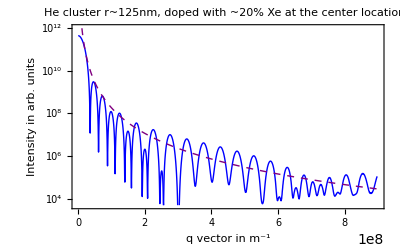

```mathematica
ListLogPlot[{Transpose[{xVal,HeXeOneScattererSum^2}],Table[N[{q,Aa(2 π)/q^4}/.Aa->0.3 10^40],{q,1,9 10^8,10^6}]},Joined->True,
Frame->True,PlotStyle->{Directive[Blue],Directive[Thick,Dashed,Purple],Table[{q,guneqn}/.{r->125 10^-9,Aaa->0.7 10^9},{q,1,9 10^8,10^6}],Directive[Thick,Dashed,Black],Directive[{Red,Thick}],Directive[{Red,Thick}]},FrameLabel->{"q vector in m^-1","Intensity in arb. units"},FrameStyle->Directive[12],PlotLegend->{"HeXe intact",  "Scattering from sphere r=202nm","∝ q^-4"},LegendPosition->{0.11,0.25},LegendShadow->None,LegendSize->{0.7,0.3},LegendTextSpace->4,
PlotLabel->"He cluster r~125nm, doped with ~20% Xe at the center locations",PlotRange->{{1,9 10^8},{0.5 10^4,0.01 10^14}}]
```